```mathematica
Clear["Global`*"]
Needs["ToMatlab`"]
```

Needs::nocont: Context ToMatlab` was not created when Needs was evaluated.

```mathematica
dmrnadt[d_, R_, kd_, n_] = R * (  (d/kd)^n/(1+(d/kd)^n) )
```

((d/kd)^n R)/(1+(d/kd)^n)

```mathematica
Manipulate[Plot[dmrnadt[d, R, kd], {d, 1, 3000}], {R, 1, 100}, {kd, 1, 3000}]
```

```mathematica
(*dmRNAdtDist[d_, L_, R_, kd_, n_, v_] = TruncatedDistribution[{0, ∞},NormalDistribution[dmrnadt[d, R, kd, n],v*dmrnadt[d, R, kd, n]]]*)
```

```mathematica
dmRNAdtDist[d_, L_, R_, kd_, n_, v_] = TruncatedDistribution[{0, ∞},LogNormalDistribution[Log[dmrnadt[d, R, kd, n]]-(0.5*v^2),v]]
```

LogNormalDistribution[-0.5 v^2+Log[((d/kd)^n R)/(1+(d/kd)^n)],v]

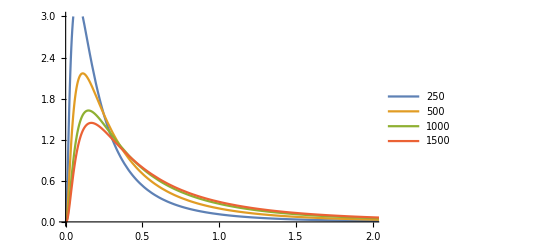

```mathematica
Plot[Table[PDF[dmRNAdtDist[d, 0, 1, 500, 1, 1],x],{d,{250, 500, 1000, 1500}}]//Evaluate,{x,0, 10}, PlotLegends-> {250, 500, 1000, 1500}, PlotRange->{{0,2},{0, 3}}]
```

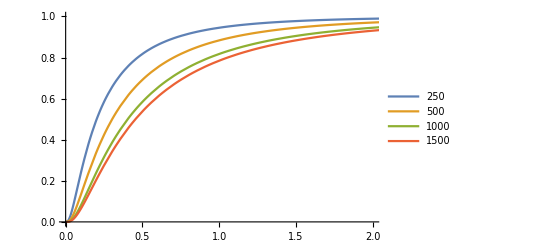

```mathematica
Plot[Table[CDF[dmRNAdtDist[d, 0, 1, 500, 1, 1],x],{d,{250, 500, 1000, 1500}}]//Evaluate,{x,0, 10}, PlotLegends-> {250, 500, 1000, 1500}, PlotRange->{{0,2},{0, 1}}]
```

```mathematica
pactive[d_, L_, R_, kd_, n_, v_] = 1  - CDF[dmRNAdtDist[d, L, R, kd, n, v],L]
```

1-(Piecewise[{{1/2 Erfc[(-0.5 v^2-Log[L]+Log[((d/kd)^n R)/(1+(d/kd)^n)])/(√2 v)], L>0}, {0, True}}])

```mathematica
Remove[f1]
```

```mathematica
Remove[f2]
```

```mathematica
f1[L_, R_, kd_, n_, v_] := Plot[pactive[d,L, R, kd, n, v], {d, 1, 3000}, PlotStyle->Green, PlotLegends->{"fraction active"}, PlotRange->{{0 ,3000}, {0, 1}}];
f2[R_, kd_, n_] := Plot[dmrnadt[d, R, kd, n], {d, 1, 3000}, PlotStyle->Blue, PlotLegends->{"dmRNA/dt"}];
Manipulate[Show[f1[L, R, kd, n, v], f2[R,kd, n]], {R, 1, 1}, {kd, 500, 3000}, {L, 0, 1}, {n, 1, 6}, {v, .01, 10}]
```

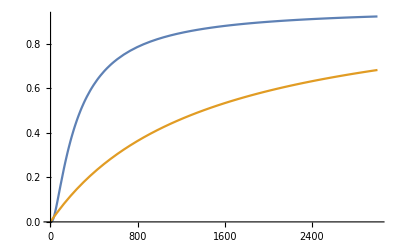

```mathematica
Show[Table[Plot[{pactive[d,L, R, kd, n, v]/.{R->1, n->1, v->1, kd->1400}, dmrnadt[d, R,kd, n] /.{R->1, n->1,kd->1400}}, {d, 1, 3000}],{L, .1, .2, .3}]]
```